### Settings

```mathematica
d=2;
a=8;
delta = 1;
rMax=20; 
Z =0.125; 
coord = {{0,0},{d,0}, {-d, 0}, {2*d, 0}, {-2*d, 0}, {-3*d, 0} , {3*d, 0}};
```

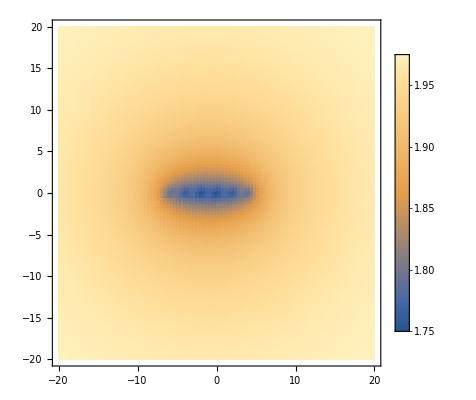

```mathematica
V[x_, y_] := Sum[(-Z)/(Sqrt[(x- coord[[i]][[1]])^2  + (y-coord[[i]][[2]])^2]+delta)(**Exp[-Sqrt[(x-coord[[i]][[1]])^2  + (y-coord[[i]][[2]])^2]/a] *),{i,6} ] +2  ;
DensityPlot[V[x ,y],{x,-rMax,rMax},{y,-rMax,rMax}, (*PlotTheme->"Minimal",*) PlotPoints->100,  PlotLegends->Automatic, PlotRange->All]
(*Export[NotebookDirectory[]<>"Coulomb.png",%,ImageResolution->100];*)
```

```mathematica
|
```

### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/2)* Laplacian[R2D[x,y],{x,y},"Cartesian"]+V[x,y]*R2D[x,y]
,DirichletCondition[R2D[x,y]==0,x==-rMax || x==rMax || y==-rMax || y==rMax]},
R2D[x,y],{x,-rMax,rMax},{y,-rMax,rMax},8, Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->1000000}(* "Direct"*),"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}  ];
ord =Ordering[egnVal];
Sort[Re[egnVal]]
```

{1.86454,1.91485,1.93698,1.95118,1.96466,1.96469,1.97188,1.97956}

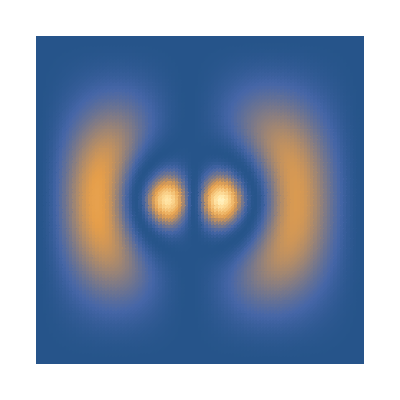

```mathematica
F1 =Part[Re[egnVec],Part[ord,7]]^2;
DensityPlot[F1,{x,-rMax,rMax},{y,-rMax,rMax}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All  (*PlotLegends->Automatic*)]
```